```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
<<Scrabbology`
```

### Check for Perfection

```mathematica
store=CloudGet["PerfectScrabbleGames"];
```

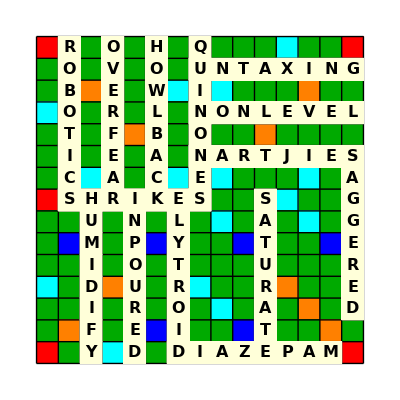

{True,Blanks: | {R,R}
 Leftovers: | {E,W}}

```mathematica
game=RandomChoice[store];
board=CreateInitialScrabbleBoard[];
Show[board,Epilog->GameToEpilog[game]]
PerfectScrabbleGameQ[game]
Dataset[game]
```

```mathematica
PerfectScrabbleGameQ/@store
```

{{True,Blanks: | {H,N}
 Leftovers: | {J,P}},{True,Blanks: | {K,X}
 Leftovers: | {A,Q}},{True,Blanks: | {R}
 Leftovers: | {J}},{True,Blanks: | {A,I}
 Leftovers: | {B,E}},{True,Blanks: | {G,L}
 Leftovers: | {E,U}},{True,Blanks: | {O,T}
 Leftovers: | {A,F}},{True,Blanks: | {E,R}
 Leftovers: | {A,O}},{True,Blanks: | {C,I}
 Leftovers: | {E,W}},{True,Blanks: | {R}
 Leftovers: | {J}},{True,Blanks: | {H,R}
 Leftovers: | {A,J}},{True,Blanks: | {O,S}
 Leftovers: | {E,P}},{True,Blanks: | {R,R}
 Leftovers: | {E,W}},{True,Blanks: | {I,S}
 Leftovers: | {N,Z}},{True,Blanks: | {G,S}
 Leftovers: | {T,Y}},{True,Blanks: | {L,Z}
 Leftovers: | {E,I}},{True,Blanks: | {C,W}
 Leftovers: | {E}},{True,Blanks: | {C,R}
 Leftovers: | {J,O}},{True,Blanks: | {B,R}
 Leftovers: | {E,F}},{True,Blanks: | {M,M}
 Leftovers: | {H,Q}}}

## To Do

Function for inserting a blank at position X

Function for generating Epilog and Tiles state to be animated.